# The Traveling Salesman Problem

Finding the optimal tour through cities in Mexico.

Luis Fernando Cantú, Jun. 29,  2018

The Traveling Salesman Problem (TSP) is a famous problem in combinatorial optimization. The TSP is simple to state: given a list of cities and the distances between each of them, finding which is the shortest possible route that visits all of the cities and returns to the origin. It has been demonstrated to be NP- complete, which means that an exact polynomial time solution to the problem for large n has not been found. The TSP has been studied not only because of its real-world applicability, but also because finding a polynomial time solution for it would mean the P versus NP problem would be solved for good.

## Explaining the Problem

Suppose you are on a business trip in Mexico and would like to visit some of the most populated cities in the country.

Let’s see some of the most populated cities in the country:

```mathematica
mexicanMunicipalities = CityData[{Large, "Mexico"}]  // (Take[#,{1,16,2}]&)
```

{Mexico City,Tijuana,Guadalajara,Juarez,Monterrey,Aguascalientes,Naucalpan,San Luis Potosi}

Mexico City tops the list, of course. But we are not visiting these cities according to the size of their population, but rather by minimizing the total trip distance. So let’s see where these cities are located.

In the figure below, the red points represent the locations of  each element in the list mexicanMunicipalities:

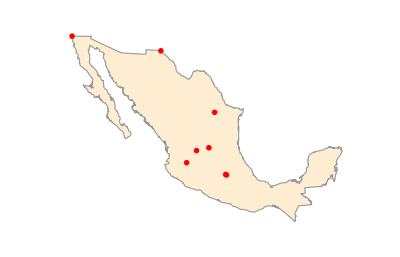

```mathematica
GeoGraphics[{GeoStyling["OutlineMap"],EdgeForm[Black],
Polygon[LinguisticAssistant],Red,PointSize[0.01],
Point[mexicanMunicipalities]},GeoBackground->None]
```

Remember that your trip can begin in any of the cities marked by the red points, but it must also end in the same place where your tour started.

This is how it would look like if you were to begin your trip from any of the cities selected.

```mathematica
Manipulate[GeoGraphics[],, SaveDefinitions->True]
```

We can now see where the problem lies. Starting from any point, we can travel to any of the remaining cities. If there are n cities, that means there are n-1 different options where to go next. In the next step of the process there will be n-2 options, and so on. We could try to solve the problem by exploring all the available routes, but with a sufficiently large number of cities, this could take many millions of years.

Time it would take to find the optimal solution using the brute force approach, assuming 1,000,000 routes could be checked every second:

```mathematica
Manipulate[Quantity[(n-1)!/(2*1000000.), "Seconds"]//UnitConvert[#,"Millennia"]& ,Style["Choose the number of cities:", Bold, Medium],{n,1,200,1}]
```

This should be enough to convince us that the brute force approach is not the right way to optimize. There are other exact algorithms that could give us the solution in exponential time, but here we will focus on approximate heuristics.

## Greedy Algorithm

Now, one of the first ideas that might come to your mind would be, starting from any city, to find its nearest neighbor, move towards it, and then repeat the whole process again. This is a greedy algorithm, since it follows the locally optimal choice at each node in the network.

Here are the distances between every municipality considered in our analysis:

```mathematica
matrix = DistanceMatrix[mexicanMunicipalities];
cityToDistance = Association[Thread[mexicanMunicipalities->matrix⟦#⟧]]&/@Range[Length[mexicanMunicipalities]]
```

{<|Mexico City→0. mi,Tijuana→1428.2 mi,Guadalajara→286.638 mi,Juarez→962.91 mi,Monterrey→435.936 mi,Aguascalientes→265.074 mi,Naucalpan→6.80513 mi,San Luis Potosi→222.345 mi|>,<|Mexico City→1428.2 mi,Tijuana→0. mi,Guadalajara→1173.61 mi,Juarez→619.504 mi,Monterrey→1113.34 mi,Aguascalientes→1163.48 mi,Naucalpan→1421.56 mi,San Luis Potosi→1215.03 mi|>,<|Mexico City→286.638 mi,Tijuana→1173.61 mi,Guadalajara→0. mi,Juarez→786.521 mi,Monterrey→394.353 mi,Aguascalientes→107.304 mi,Naucalpan→279.994 mi,San Luis Potosi→183.899 mi|>,<|Mexico City→962.91 mi,Tijuana→619.504 mi,Guadalajara→786.521 mi,Juarez→0. mi,Monterrey→561.077 mi,Aguascalientes→726.324 mi,Naucalpan→957.191 mi,San Luis Potosi→741.716 mi|>,<|Mexico City→435.936 mi,Tijuana→1113.34 mi,Guadalajara→394.353 mi,Juarez→561.077 mi,Monterrey→0. mi,Aguascalientes→289.393 mi,Naucalpan→431.583 mi,San Luis Potosi→245.144 mi|>,<|Mexico City→265.074 mi,Tijuana→1163.48 mi,Guadalajara→107.304 mi,Juarez→726.324 mi,Monterrey→289.393 mi,Aguascalientes→0. mi,Naucalpan→258.367 mi,San Luis Potosi→86.8481 mi|>,<|Mexico City→6.80513 mi,Tijuana→1421.56 mi,Guadalajara→279.994 mi,Juarez→957.191 mi,Monterrey→431.583 mi,Aguascalientes→258.367 mi,Naucalpan→0. mi,San Luis Potosi→216.337 mi|>,<|Mexico City→222.345 mi,Tijuana→1215.03 mi,Guadalajara→183.899 mi,Juarez→741.716 mi,Monterrey→245.144 mi,Aguascalientes→86.8481 mi,Naucalpan→216.337 mi,San Luis Potosi→0. mi|>}

Each association must be sorted according to the distance it takes to reach other cities:

```mathematica
sortCities[association_]:= SortBy[association, First];
cityDistanceMap = sortCities /@ cityToDistance
```

{<|Mexico City→0. mi,Naucalpan→6.80513 mi,San Luis Potosi→222.345 mi,Aguascalientes→265.074 mi,Guadalajara→286.638 mi,Monterrey→435.936 mi,Juarez→962.91 mi,Tijuana→1428.2 mi|>,<|Tijuana→0. mi,Juarez→619.504 mi,Monterrey→1113.34 mi,Aguascalientes→1163.48 mi,Guadalajara→1173.61 mi,San Luis Potosi→1215.03 mi,Naucalpan→1421.56 mi,Mexico City→1428.2 mi|>,<|Guadalajara→0. mi,Aguascalientes→107.304 mi,San Luis Potosi→183.899 mi,Naucalpan→279.994 mi,Mexico City→286.638 mi,Monterrey→394.353 mi,Juarez→786.521 mi,Tijuana→1173.61 mi|>,<|Juarez→0. mi,Monterrey→561.077 mi,Tijuana→619.504 mi,Aguascalientes→726.324 mi,San Luis Potosi→741.716 mi,Guadalajara→786.521 mi,Naucalpan→957.191 mi,Mexico City→962.91 mi|>,<|Monterrey→0. mi,San Luis Potosi→245.144 mi,Aguascalientes→289.393 mi,Guadalajara→394.353 mi,Naucalpan→431.583 mi,Mexico City→435.936 mi,Juarez→561.077 mi,Tijuana→1113.34 mi|>,<|Aguascalientes→0. mi,San Luis Potosi→86.8481 mi,Guadalajara→107.304 mi,Naucalpan→258.367 mi,Mexico City→265.074 mi,Monterrey→289.393 mi,Juarez→726.324 mi,Tijuana→1163.48 mi|>,<|Naucalpan→0. mi,Mexico City→6.80513 mi,San Luis Potosi→216.337 mi,Aguascalientes→258.367 mi,Guadalajara→279.994 mi,Monterrey→431.583 mi,Juarez→957.191 mi,Tijuana→1421.56 mi|>,<|San Luis Potosi→0. mi,Aguascalientes→86.8481 mi,Guadalajara→183.899 mi,Naucalpan→216.337 mi,Mexico City→222.345 mi,Monterrey→245.144 mi,Juarez→741.716 mi,Tijuana→1215.03 mi|>}

Now we create two different functions to find the nearest neighbor without including cities we have visited before. This will return us the path we would take if we always went for the nearest neighbor in each city:

```mathematica
findCityPositionInCityDistanceMap[cityDistanceMap_, city_]:= Module[]
nearestNeighbor[start_, cities_, cityDistanceMap_List]:= Module[]
```

Here’s the path we would follow if we started in Mexico City and always went for the nearest neighbor :

```mathematica
byNearestMunicipality = nearestNeighbor[Entity["City",{"MexicoCity","DistritoFederal","Mexico"}], mexicanMunicipalities, cityDistanceMap]
```

{Mexico City,Naucalpan,San Luis Potosi,Aguascalientes,Guadalajara,Monterrey,Juarez,Tijuana,Mexico City}

It is easier to visualize the last result in a map:

```mathematica
nearestPairing=Table[{byNearestMunicipality⟦n⟧,byNearestMunicipality⟦n+1⟧},{n,1,Length[mexicanMunicipalities]}];
Manipulate[GeoGraphics[Sequence[{,Arrow[nearestPairing⟦1;;n⟧]},GeoBackground->None]],]
```

Here’s the path we would follow if we started in Aguascalientes and always went for the nearest neighbor :

```mathematica
byNearestMunicipality2 = nearestNeighbor[Entity["City",{"Aguascalientes","Aguascalientes","Mexico"}], mexicanMunicipalities, cityDistanceMap]
```

{Aguascalientes,San Luis Potosi,Guadalajara,Naucalpan,Mexico City,Monterrey,Juarez,Tijuana,Aguascalientes}

Once again, it is easier to visualize the tour in a map:

```mathematica
nearestPairing2=Table[{byNearestMunicipality2⟦n⟧,byNearestMunicipality2⟦n+1⟧},{n,1,Length[mexicanMunicipalities]}];
Manipulate[GeoGraphics[Sequence[{,Arrow[nearestPairing2⟦1;;n⟧]},GeoBackground->None]],]
```

Looking at the two previous animations it is straightforward to see that, even though we act in accordance with the same greedy algorithm, the route is different and changes depending on the initial point.

If you start in Mexico City and always go for the nearest neighbor, you would travel:

```mathematica
GeoDistanceList[byNearestMunicipality] // Total
```

3420.43 mi

If you start in Aguascalientes and always go for the nearest neighbor, you would travel:

```mathematica
GeoDistanceList[byNearestMunicipality2] // Total
```

3337.55 mi

This shows that the route starting from Aguascalientes is shorter than the one starting from Mexico City.

## Minimum Spanning Tree

In our context, a Minimum Spanning Tree (MST)is a subset of the roads between cities that connects all of them together, without forming any cycles, and with the smallest possible total distance. There are several algorithms that return a MST, but we will focus on Prim’s algorithm, described below.

Prim's algorithm:
    let T be a single vertex x
    while (T has fewer than n vertices)
    {
        find the smallest edge connecting T to G-T
        add it to T
    }

First, we will need to create a graph with each city as a vertex and the distances as edges.

First, we need the coordinates of the cities:

```mathematica
posMex = GeoPosition[#["Coordinates"]]&/@mexicanMunicipalities
```

{GeoPosition[{19.43,-99.14}],GeoPosition[{32.53,-117.02}],GeoPosition[{20.67,-103.35}],GeoPosition[{31.74,-106.49}],GeoPosition[{25.67,-100.32}],GeoPosition[{21.88,-102.3}],GeoPosition[{19.48,-99.23}],GeoPosition[{22.16,-100.98}]}

Now we create and adjacency matrix and a WeightedAdjacencyGraph:

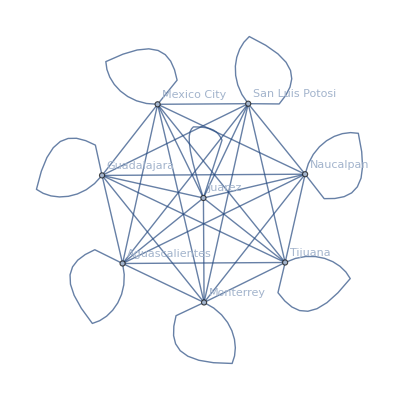

```mathematica
adj=Table[QuantityMagnitude@GeoDistance[i,j],{i,posMex},{j,posMex}];
g=WeightedAdjacencyGraph[mexicanMunicipalities,adj, VertexLabels->All, DirectedEdges->False]
```

Using Prim’s algorithm, we can get the Minimum Spanning Tree of the previous graph:

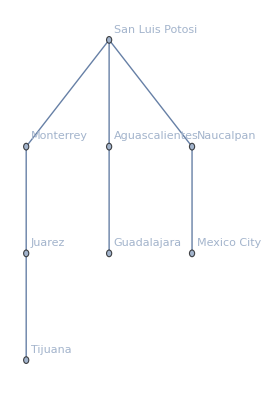

```mathematica
mst= FindSpanningTree[g, VertexLabels->All, Method->"Prim"]
```

We can see from the graph above that our job is almost done.

## Filling the MST gaps

After using Prim’s algorithm, we only need to fill in the gaps. To find our tour, we will follow the well known Christofides Algorithm. First we need to calculate the set of vertices O with odd degree in the MST.

We can get the degree of all vertices with the VertexDegree function:

```mathematica
VertexList[mst]
```

{Mexico City,Tijuana,Guadalajara,Juarez,Monterrey,Aguascalientes,Naucalpan,San Luis Potosi}

```mathematica
VertexDegree[mst]
```

{1,1,1,2,2,2,2,3}

We form the Subgraph of graph g using only the odd vertices of the list above:

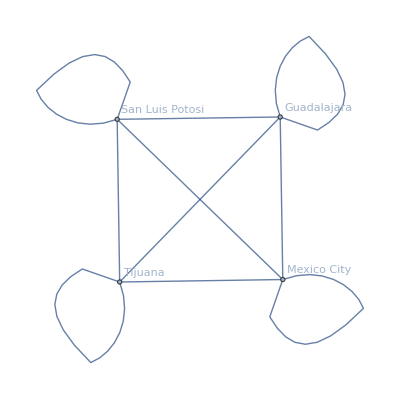

```mathematica
Subgraph[g, VertexList[mst][[{1,2,3,8}]], VertexLabels->All]
```

Now, we construct a minimum-weight perfect matching m in the subgraph above:

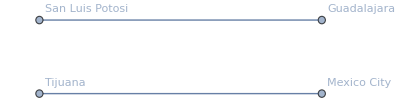

```mathematica
(m = FindIndependentEdgeSet[%]) // Graph[#,VertexLabels->All]&
```

The MST and the perfect matching m are united:

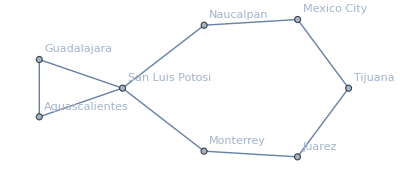

```mathematica
Join[mst//EdgeList, m] // Graph[#,VertexLabels->All]&
```

We calculate the Euler tour:

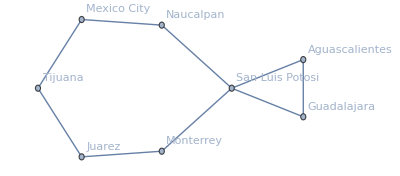

```mathematica
FindEulerianCycle[%]// Flatten // Graph[#,VertexLabels->All]&
```

By the look of the last graph, it seems that we already had the Euler tour.

We remove duplicate vertices:

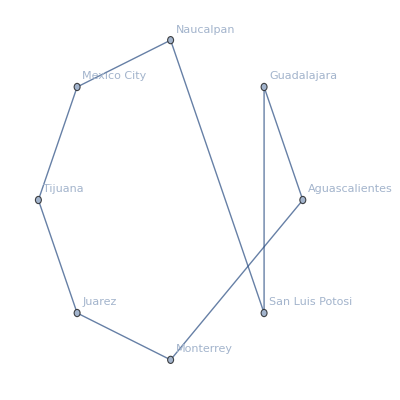

```mathematica
EdgeDelete[%,{Entity["City",{"Aguascalientes","Aguascalientes","Mexico"}]<-> Entity["City",{"SanLuisPotosi","SanLuisPotosi","Mexico"}], Entity["City",{"SanLuisPotosi","SanLuisPotosi","Mexico"}]<->Entity["City",{"Monterrey","NuevoLeon","Mexico"}]}];
EdgeAdd[%, Entity["City",{"Aguascalientes","Aguascalientes","Mexico"}]<->Entity["City",{"Monterrey","NuevoLeon","Mexico"}]]
```

Now we have the path we should follow.

This means that, assuming the trip starts in Mexico City, then we would visit the other cities in the following order: {"Mexico City","Naucalpan","San Luis Potosi", "Guadalajara","Aguascalientes","Monterrey","Juarez","Tijuana","Mexico City"}

This is the trip’s total distance:

```mathematica
mstTrip ={Entity["City",{"MexicoCity","DistritoFederal","Mexico"}],Entity["City",{"Naucalpan","Mexico","Mexico"}],Entity["City",{"SanLuisPotosi","SanLuisPotosi","Mexico"}], Entity["City",{"Guadalajara","Jalisco","Mexico"}],Entity["City",{"Aguascalientes","Aguascalientes","Mexico"}],Entity["City",{"Monterrey","NuevoLeon","Mexico"}],Entity["City",{"Juarez","Chihuahua","Mexico"}],Entity["City",{"Tijuana","BajaCalifornia","Mexico"}],Entity["City",{"MexicoCity","DistritoFederal","Mexico"}]};
GeoDistance@mstTrip
```

3412.52 mi

Here’s the map of the tour:

```mathematica
mstPairing=Table[{mstTrip⟦n⟧,mstTrip⟦n+1⟧},{n,1,Length[mexicanMunicipalities]}];
Manipulate[GeoGraphics[Sequence[{,Arrow[mstPairing⟦1;;n⟧]},GeoBackground->None]],]
```

The Christofides Algorithm guarantees its solutions will be at most 50% larger than the optimal solution.

## Using the Wolfram Language’s Built-in Function

Fortunately, there is a built-in function in the Wolfram Language that gives us the result we want.

Using the WL’s built-in function:

```mathematica
shortestTourIndex = FindShortestTour[posMex, PerformanceGoal->"Quality"]
```

{3194.15 mi,{1,7,6,3,2,4,5,8,1}}

Finding the coordinates:

```mathematica
shortestTour = Table[{mexicanMunicipalities⟦shortestTourIndex⟦2⟧⟦n⟧⟧,mexicanMunicipalities⟦shortestTourIndex⟦2⟧⟦n+1⟧⟧}, {n,1,Length[posMex]}]
```

{{Mexico City,Naucalpan},{Naucalpan,Aguascalientes},{Aguascalientes,Guadalajara},{Guadalajara,Tijuana},{Tijuana,Juarez},{Juarez,Monterrey},{Monterrey,San Luis Potosi},{San Luis Potosi,Mexico City}}

Here’s the map of the tour using FindShortestTour:

```mathematica
mstPairing=Table[{mstTrip⟦n⟧,mstTrip⟦n+1⟧},{n,1,Length[mexicanMunicipalities]}];
Manipulate[GeoGraphics[Sequence[{,Arrow[shortestTour⟦1;;n⟧]},GeoBackground->None]],]
```

## Further explorations

Investigate the relationship between Hamiltonian Cycles and the Traveling Salesman Problem

Delve into other NP-complete or NP-hard problems

## Author contact information

lf.cantudiaz@gmail.com